```mathematica
(*Тут входные данные*)
s[t_]:=Exp[-t] (*Исходный сигнал*)
h:={0.131,0.229,0.268,0.211,0.111,0.039,0.009,0.001} (*Импульсный отклик*)
σ:=0.005 (*Дисперсия нормального шума*)
f:=10 (*Частота дискретизации сигнала*)
t:=5(*Конец интервала сигнала*)
```

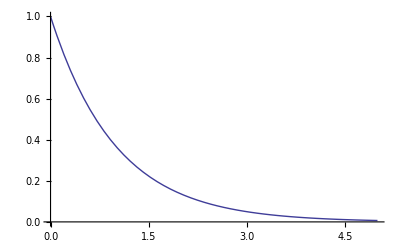

```mathematica
(*График исходного сигнала*)
Plot[s[τ],{τ,0,t}]
```

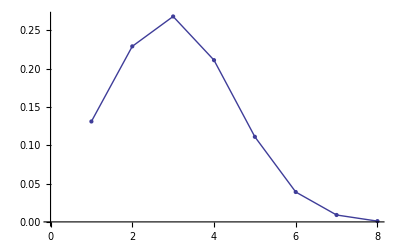

```mathematica
(*График импульсного отклика*)
ListPlot[h,{Joined->True,Mesh->All}]
```

```mathematica
(*Находим корни полинома из коэффициентов h(n) *)
poly=0;
For[i=0,i<Length[h],i++,
poly=poly+x^i*h[[i+1]]
]
poly
roots=NSolve[poly,x]
```

0.131+0.229 x+0.268 x^2+0.211 x^3+0.111 x^4+0.039 x^5+0.009 x^6+0.001 x^7

{{x→-3.22956},{x→-1.82772-0.901534 ⅈ},{x→-1.82772+0.901534 ⅈ},{x→-0.827892-2.33217 ⅈ},{x→-0.827892+2.33217 ⅈ},{x→-0.229607-1.24175 ⅈ},{x→-0.229607+1.24175 ⅈ}}

```mathematica
(*Находим модули корней*)
Abs[x]/.roots
```

{3.22956,2.03797,2.03797,2.47476,2.47476,1.2628,1.2628}

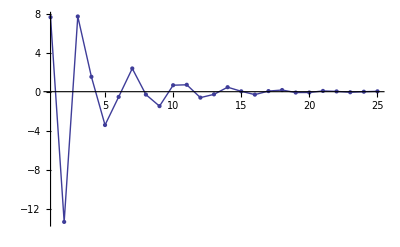

```mathematica
(*Находим hi(t) - инверсию импульсного отклика*)
hi={1/h[[1]]};
For[i=1,i≤3Length[h],i++,
sum=0;
For[k=0,k<i,k++,
If[i-k<Length[h],sum=sum+hi[[k+1]]*h[[i-k+1]]]
]
AppendTo[hi,-sum/h[[1]]]
]
ListPlot[hi,{PlotRange->All,Mesh->All,Joined->True}]
```

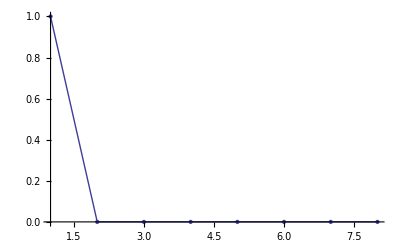

```mathematica
(*Получение свёртки сигнала h(n) с hi(k)*)
hhi={};
For[i=0,i<Length[h],i++,
sum=0;
For[k=0,k≤i,k++,
If[i-k<Length[hi],sum+=h[[k+1]]*hi[[i-k+1]]]
];
AppendTo[hhi,sum]
]
ListPlot[hhi,{PlotRange->All,Joined->True,Mesh->All}]
```

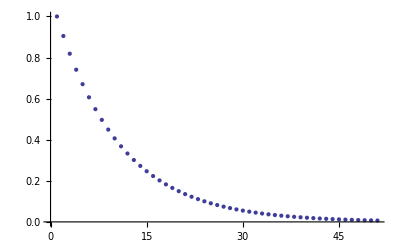

```mathematica
(*Дискретизация исходного сигнала s(t)*)
ds=Table[s[τ],{τ,0,t,1/f}];
ListPlot[ds]
```

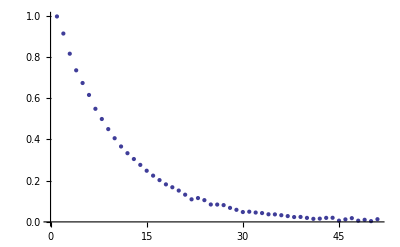

```mathematica
(*Добавление к сигналу шума*)
dsn={};
For[i=1,i≤Length[ds],i++,
AppendTo[dsn,ds[[i]]+RandomVariate[NormalDistribution[0,σ]]]
]
ListPlot[dsn]
```

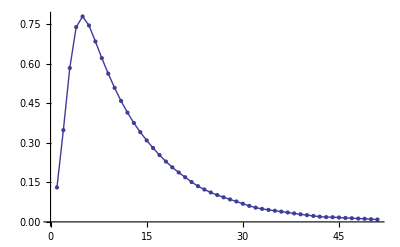

```mathematica
(*Свёртка дискретизованного сигнала s(t) с h(n)*)
sh={};
For[i=0,i<Length[hl],i++,
sum=0;
For[k=0,k≤i,k++,
If[i-k<Length[dsn],sum+=hl[[k+1]]*dsn[[i-k+1]]]
];
AppendTo[sh,sum]
]
ListPlot[sh,{Joined->True,Mesh->All}]
```

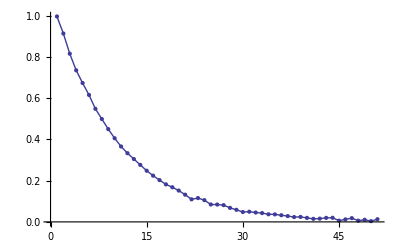
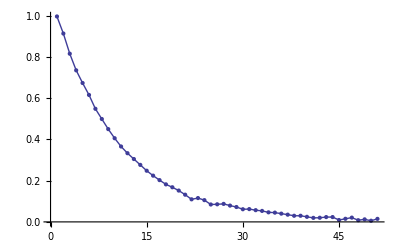

```mathematica
(*Проводим деконволюцию*)
shhi={};
For[i=0,i<Length[sh],i++,
sum=0;
For[k=0,k≤i,k++,
If[i-k<Length[hi],sum+=sh[[k+1]]*hi[[i-k+1]]]
];
AppendTo[shhi,sum]
]
Row[{ListPlot[dsn,{Joined->True,Mesh->All}],ListPlot[shhi,{Joined->True,Mesh->All}]}]
```